# Bernstein-Vazirani Algorithm

We will discuss Bernstein-Vazirani algorithm. Bernstein–Vazirani finds a hidden n-bit string using one oracle call instead of n. Prepare the n input qubits in equal superposition and the extra “answer” qubit in a state that turns flips into phases. Query the bit oracle once; its action doesn’t store information in the answer qubit but kicks back a phase pattern onto the inputs that encodes the hidden string. Apply Hadamards to convert that phase pattern into a single basis state corresponding to the hidden string. Measure the inputs and read the string with certainty. The speedup comes from superposition, phase kickback, and interference, reducing queries from n to one.

## Key Concepts

Oracle function

Bernstein-Vazirani (BV) Algorithm

## Statement of the Bernstein-Vazirani Problem

In many computer science problems, it is common to assume there is some kind of oracle function that is used in order to compute partial results for use in the rest of an algorithm. In practice, the oracle could be a database query or some similar operation.

The Bernstein–Vazirani algorithm is a quantum algorithm for a specific “oracle problem.” We are given a black-box oracle (a function) that returns the dot product (modulo 2) of an unknown binary string s with an input binary string x. The goal is to determine the unknown string s. The problem can be stated formally as follows:

There is a secret sequence, s, of length n, consisting of ones and zeros. Formally, s∈{0,1}^n.

There is an oracle, f, which accepts a sequence, x, of length n and returns the dot product of x and s modulo 2. Formally, f:{0,1}^n↦{0,1} such that f(x)=x·s mod 2.

The goal is to find the secret sequence, s, with as few uses of the oracle function f as possible.

The classical oracle function can be implemented in a straightforward way:

## Classical Bernstein-Vazirani Solution

You may try several methods, but finding the secret string of length n requires at least n queries to a classical oracle. A simple strategy is to query the oracle on each input that has exactly one 1 and the rest 0. One query to the oracle on input e_i (the unit vector with a single 1 in position i) returns s_i. To learn all n bits, any deterministic, and any bounded-error randomized, classical algorithm needs n queries in the worst case. Each query returns only one bit, namely the dot product s·x (mod 2) , so you cannot learn more than one independent bit of s per query.

Let’s consider a secret sequence of 0 and 1:

```mathematica
secret=;
```

Find the result of the oracle on input e_i through 3 queries:

```mathematica
result=Module[{queries,res,counter},
queries={{1,0,0},{0,1,0},{0,0,1}};
counter=0;
Table[
res=Mod[q.secret,2];
Echo[((((IntegerName[++counter,"Ordinal"]<>" query: ")<>ToString[q])<>" ⇒ ")<>"result: ")<>ToString[res]];
res,
{q,queries}
]
]
```

first query: {1, 0, 0} ⇒ result: 1

second query: {0, 1, 0} ⇒ result: 0

third query: {0, 0, 1} ⇒ result: 1

{1,0,1}

Check that the result is the same as the secret code:

```mathematica
result==secret
```

True

## Quantum Bernstein-Vazirani Algorithm

In the quantum version of the algorithm, the oracle will also depend on the secret sequence. This is no different from the classical oracle. But the BV algorithm needs 1 query to the oracle and recovers all n bits with certainty.

In order to create the quantum BV oracle for secret sequence of length n, you will need n+1 qubits. The last qubit, n+1-th one, is usually called as the answer qubit. For each 1 in the secret sequence, the oracle applies a CNOT gate with control qubit corresponding to that one’s place in the secret sequence and target qubit corresponding to the n+1 qubit.

Recall the secret sequence from before:

```mathematica
secret
```

{1,0,1}

The quantum BV oracle for this sequence is given by:

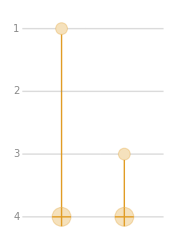

```mathematica
QuantumCircuitOperator["BernsteinVaziraniOracle"[secret]]["Diagram",ImageSize->Small]
```

So let’s remind ourself: the first n-qubits are called register or input or query qubits. The last one (n+1-th qubit) is commonly called the answer qubit, also seen as output/response qubit, target qubit, or ancilla/work qubit.

The above bit oracle acts as U_f xy=xy⊕f_s(x) where x represents n-qubit case and y the last one (usually called as the answer qubit)

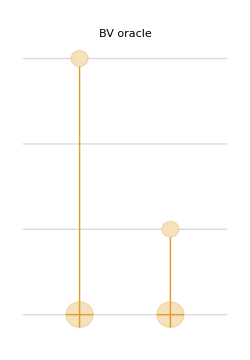
-Graphics-  xy | BVxy | xy⊕f_s(x)
0000 | 0000 | {0,0,0,0}
0001 | 0001 | {0,0,0,1}
0010 | 0011 | {0,0,1,1}
0011 | 0010 | {0,0,1,0}
0100 | 0100 | {0,1,0,0}
0101 | 0101 | {0,1,0,1}
0110 | 0111 | {0,1,1,1}
0111 | 0110 | {0,1,1,0}
1000 | 1001 | {1,0,0,1}
1001 | 1000 | {1,0,0,0}
1010 | 1010 | {1,0,1,0}
1011 | 1011 | {1,0,1,1}
1100 | 1101 | {1,1,0,1}
1101 | 1100 | {1,1,0,0}
1110 | 1110 | {1,1,1,0}
1111 | 1111 | {1,1,1,1}

```mathematica
With[{op=QuantumCircuitOperator["BernsteinVaziraniOracle"[secret]]},Row[{op["Diagram","WireLabels"->None,ImageSize->250,PlotLabel->"BV oracle"],"  ",TableForm[Transpose[Append[Transpose[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,4]["BasisStates"]],Riffle[Append[#,BitXor[Mod[secret.#,2],0]]&/@Tuples[{0,1},Length[secret]],Append[#,BitXor[Mod[secret.#,2],1]]&/@Tuples[{0,1},Length[secret]]]]],TableHeadings->{None, {"xy","BVxy","xy⊕f_s(x)"}},TableDepth->2]}]]
```

In the context of the problem, you might imagine that this oracle is a quantum device which is networked to the rest of your circuit but which you cannot directly “see” (otherwise the gate structure of the oracle immediately gives away the answer).

In order to use this oracle to discover the secret code, only one query is necessary. Using the phenomenon of phase kickback, it is possible to send a uniform superposition of all possible sequences (as measured in the computational basis) and encode the solution in the three control qubits.

The full circuit would look like this:

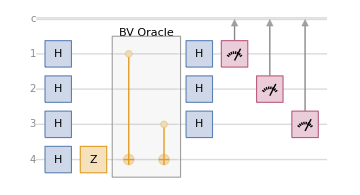

```mathematica
bv=QuantumCircuitOperator["BernsteinVazirani"[secret]];
bv["Diagram"]
```

Phase kickback is the mechanism by which a conditional action on a target (when the target sits in an eigenstate) becomes a conditional phase on the control. In BV, CNOTs into an answer qubit prepared as - kick back the parity f(x)=s⋅x as a phase (-1)^(f(x)) on x. Two Hadamard layers then turn that phase pattern into the deterministic answer s.

Let’s monitor the state evolution in the BV circuit. Before the oracle, the n-qubits are in a uniform superposition, and the answer qubit is in the minus state x_-.

```mathematica
step1=bv[[;;Length[secret]+2]];
step1["Diagram",ImageSize->100]
```

-Graphics-

Execute the above circuit and get the result:

```mathematica
ψ1=step1[];
QuantumState[ψ1,QuantumBasis["X",Length[secret]+1]]//TraditionalForm
```

𝓍_+𝓍_+𝓍_+𝓍_−

Let’s dive into the above code. First, we execute that a specific of the BV circuit which effective prepare an initial state. The resulting state is in the computational basis. Then we transform the state into the Pauli-X basis of n+1 basis. This is a very useful feature in the Wolfram quantum framework. You can do the basis transformation as QuantumState[ψ,QuantumBasis[...]] that transform the state ψ the new basis. Let’s look at the state before and after the basis transformation:

```mathematica
Row[{TraditionalForm[ψ1],Style["⟶",Directive[Bold,Red]],TraditionalForm[QuantumState[ψ1,QuantumBasis["X",Length[secret]+1]]]}]
```

1/4 0000-1/40001+1/4 0010-1/40011+1/4 0100-1/40101+1/4 0110-1/40111+1/4 1000-1/41001+1/4 1010-1/41011+1/4 1100-1/41101+1/4 1110-1/41111⟶𝓍_+𝓍_+𝓍_+𝓍_−

It is clear that, in the new basis, the state is represented more compactly, and the idea of a uniform superposition with the answer qubit in the minus state is made explicit.

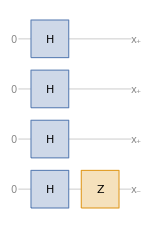

```mathematica
step1["Diagram","WireLabels"->{1->{Placed["0",Left],Placed["x_+",Right]},2->{Placed["0",Left],Placed["x_+",Right]},3->{Placed["0",Left],Placed["x_+",Right]},4->{Placed["0",Left],Placed["x_-",Right]}},ImageSize->150]
```

Now let’s examine how the BV oracle acts on the current quantum state. As discussed earlier, through the phase kickback effect, the oracle introduces a phase shift to specific terms determined by the secret string. For clarity, let’s recall the secret string: {1, 0, 1}. In this case, the oracle imprints a phase of –1 according to the function f_s(x), while the answer qubit remains unchanged.

```mathematica
QuantumState[QuantumCircuitOperator["BernsteinVaziraniOracle"[secret]][ψ1],QuantumBasis["X",Length[secret]+1]]//TraditionalForm
```

𝓍_−𝓍_+𝓍_−𝓍_−

As before, in you look at the code above, we did a basis transformation.

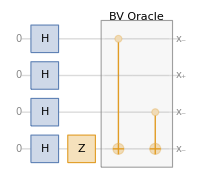

```mathematica
step2=bv[[;;-2Length[secret]-1]];
step2["Diagram","WireLabels"->{1->{Placed["0",Left],Placed["x_-",Right]},2->{Placed["0",Left],Placed["x_+",Right]},3->{Placed["0",Left],Placed["x_-",Right]},4->{Placed["0",Left],Placed["x_-",Right]}},ImageSize->200]
```

The final layer of Hadamard gates converts the phase pattern into a definite, deterministic result s.

```mathematica
step3=bv[[;;-Length[secret]-1]];
QuantumState[step3[],QuantumTensorProduct[QuantumBasis[2,Length[secret]],QuantumBasis["X"]]]//TraditionalForm
```

101 𝓍_−

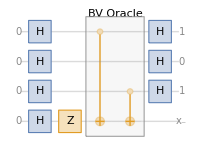

```mathematica
step3["Diagram","WireLabels"->{1->{Placed["0",Left],Placed["1",Right]},2->{Placed["0",Left],Placed["0",Right]},3->{Placed["0",Left],Placed["1",Right]},4->{Placed["0",Left],Placed["x_-",Right]}},ImageSize->200]
```

The final step is measurements. Note we only measure n-qubits.

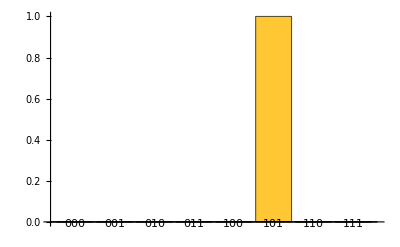

```mathematica
QuantumCircuitOperator["BernsteinVazirani"[secret]][]["ProbabilitiesPlot"]
```

Therefore, the algorithm gives the secret code in only a single query.

The key feature of the BV algorithm is that the final measurement yields a single, definite result, the secret string. While this is elegant in theory, in practice, noise can interfere with the algorithm’s performance. In the next section, we will briefly discuss the impact of noise.

## Effects of Noise

While solving the problem in only a single query to the quantum oracle is possible theoretically, real quantum circuits involve some errors caused by various effects. All of the previous circuits you have considered did not take this phenomena into account.

The following circuit defines the BV algorithm but introduces a noise channel just before the measurements can be performed. You might imagine this noise is from imperfect measurement or from the cumulative effect of previous errors in the circuit.

```mathematica
noisyBV[s_List]:=With[{n=Length[s]},
QuantumCircuitOperator[{"H"->Range[n+1],"Z"->n+1,QuantumCircuitOperator["BernsteinVaziraniOracle"[s],"BV Oracle"],"H"->Range[n+1],Splice@Table[QuantumChannel["Depolarizing"[p],{k}],{k,n+1}],"M"->Range[n]},"Parameters"->p]
]
```

A noisy version of the previous circuit might look like this:

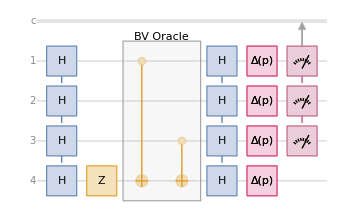

```mathematica
noisyBV[secret]["Diagram"]
```

Notice that the measurement distribution now depends on the probability of the noise channels affecting each qubit:

```mathematica
noisymeasurement=noisyBV[secret][]
```

QuantumMeasurement[…]

```mathematica
noisymeasurement["Parameters"]
```

{p}

If the so-called depolarizing noise channels affect the qubits with probability under 5%, the chance of returning the secret code is still quite high:

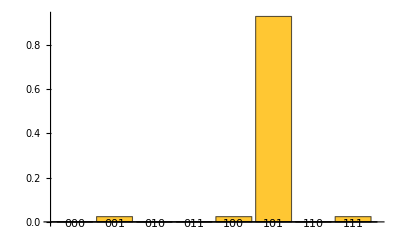

```mathematica
noisymeasurement[<|p->0.05|>]["ProbabilitiesPlot"]
```

The following animation shows the effect of increasing the depolarizing probability:

```mathematica
With[{fps=20.0,dur=2},ListAnimate[
Table[Rasterize@noisymeasurement[<|p->prob|>]["ProbabilitiesPlot",PlotRange->{0,1},PlotRangePadding->Scaled[.1]],
{prob,0,1,1/(dur*fps)}],fps,ControlPlacement->Top,AnimationRunning->False
]]
```

You can also plot all measurement outcome probabilities as a function of the depolarizing probability:

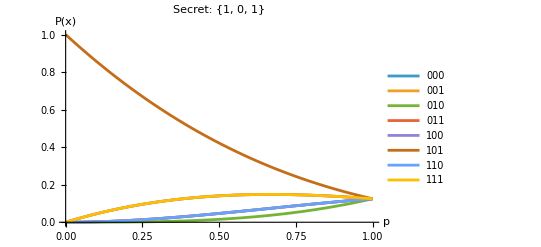

```mathematica
Plot[Evaluate@noisymeasurement[<|p->prob|>]["ProbabilitiesList"],{prob,0,1},PlotRange->All,PlotLegends->noisymeasurement["Outcomes"],PlotLabel->"Secret: "<>ToString[secret],AxesLabel->{p,P[x]}]
```

## Compensating for Errors

In practical quantum algorithms, an important consideration is the resilience of that algorithm to errors. Let’s use the noisy circuit in the last section for an example of a very simple error mitigating scheme.

First, compute the distribution of measurement outcomes for this circuit:

```mathematica
𝒟=Assuming[0<=p<=1,noisymeasurement["Simplify"]["MultivariateDistribution"]]
```

CategoricalDistribution[…]

The probability of success on each run of the circuit can be obtained:

```mathematica
sucessprob=PDF[𝒟,secret]//Simplify
```

-1/8 (-2+p)^3

One very simple way to mitigate the chance of failure is to simply run the algorithm 2k times. If k or more of the runs agree on an answer, assume that is the secret code.

Using a little probability theory, the chance of half or more of the runs failing can be computed as:

```mathematica
halfFail=Simplify[
CDF[BinomialDistribution[2k,sucessprob],k-1],
{k∈Integers,k>=1}
]
```

BetaRegularized[1+1/8 (-2+p)^3,1+k,k]

That mathematical function might look a little scary, but you can easily work with it using the Wolfram Language. It can be used like any other symbol. The plot below shows contours which relate the probability this simple error mitigation scheme failing to the probability of depolarization:

```mathematica
contourEqns=Table[ϵ==halfFail,{k,2^Range[0,7]}];
ContourPlot[contourEqns,{p,0,.3},{ϵ,10^-6,.5},ScalingFunctions->{None,"Log"},PlotPoints->50,FrameLabel->{p["depolarizing"],ϵ},PlotLabel->"ϵ: probability of half or more of the runs failing "(*ToString[TraditionalForm[ϵ==P[successes<n/2|ToString[TraditionalForm[n]]<>" trials"]]]*),PlotRangePadding->None,PlotTheme->"Web",GridLines->Automatic,GridLinesStyle->Directive[Gray,Thick,Dashed],ContourStyle->"ThermometerColors",PlotLegends->PointLegend[Automatic,Table[2^(e+1),{e,0,7}],LegendLabel->"Trials",LegendFunction->"Frame"]]//Quiet//Rasterize
```

-Graphics-

Notice that increasing the number of trials in this error mitigation scheme generally reduces the probability for the scheme to fail, even if the probability of depolarization is quite high.

The number of trials in which you run a quantum circuit is often called the number of “shots” by hardware providers. Keep in mind that any circuit which can give different results on different trials must be run more than once in order that you get a good estimate of the true measurement distribution.

You can use the "SimulatedMeasurement" property to simulate the measurement outcomes of a quantum circuit. Notice that in this experiment, the secret string was the measured outcome the majority of the time. Also notice that it is unlikely for the outcomes to be more than Hamming distance 1 away from the secret code in this experiment:

```mathematica
SeedRandom[1234];
noisymeasurement[<|p->.1|>]["SimulatedMeasurement",100]//Counts//Dataset//Rasterize
```

-Graphics-

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]